## Time-independent master equation solver Kenneth Sharman August 21, 2020 Walkthrough of Stephen Wein’s code in an attempt to learn some Mathematica in the context of quantum optics.

## Liouville Superoperator

```mathematica
(* Takes a state vector and gives the corresponding density matrix *)
ρState[ψ_] := KroneckerProduct[ψ, ψ];

(* Takes a density 'vector' in the Liouville-Fock space and transforms it back into a matrix *)
MEState[ρ_] := Partition[ρ, Sqrt[Length[ρ]]];

(* Takes a density matrix and flattens it into its vector form in the Liouville-Fock space *)
LFState[ρ_] := Flatten[ρ];

(* Takes two operators op1 and op2 acting on an operator in the Hilbert space (say ρ) as D.ρ = op1.ρ.op2 and returns the corresponding superoperator D in its matrix representation in the Lioville-Fock space *)
LFOp[op1_, op2_] := KroneckerProduct[op1, Transpose[op2]];

(* Takes a Hamiltonian and a set of collapse operators (in units of sqrt energy/frequency) and gives the Liouville superoperator in the Liouville-Fock space *)
SuperLiou[H_, collapseSet_] := Module[{IM, TP, KP, CT, MF, Lind, LComm, L},
CT=ConjugateTranspose;
IM=IdentityMatrix;
L = Length;
Lind[A_] := LFOp[A,CT[A]]-LFOp[CT[A].A,IM[L[A]]]/2-LFOp[IM[L[A]],CT[A].A]/2;
LComm[A_]:=LFOp[A,IM[L[A]]]-LFOp[IM[L[A]],A];
-ⅈ*LComm[H]+Sum[Refine[Lind[collapseSet[[i]]]],{i,L[collapseSet]}]
];

(* Takes a Liouville superoperator in its matrix representation (Liouville-Fock space) and returns the propagation superoperator in the same space *)
SuperU[Liou_,tf_,t0_] := MatrixExp[(tf-t0)*Liou];
```

### Example: Driven Lambda System

```mathematica
$Assumptions={γue>0,γde>0,γs>0,Ω>0,Δ∈Reals,χud>0,χdu>0,χs>0};

(* States *)
"u"={1,0,0};
"d"={0,1,0};
"e"={0,0,1};

(* Operators *)
σuu=KroneckerProduct["u","u"];
σdd=KroneckerProduct["d","d"];
σee=KroneckerProduct["e","e"];
σud=KroneckerProduct["u","d"];σdu=ConjugateTranspose[σud];
σue=KroneckerProduct["u","e"];σeu=ConjugateTranspose[σue];
σde=KroneckerProduct["d","e"];σed=ConjugateTranspose[σde];

(* Hamiltonian in the rotating frame of the driving laser *)
hamiltonian=Δ*σee+(Ω/2)*(σue+σeu);

(* Dissipation and dephasing *)
collapseSet={Sqrt[γue]*σue,Sqrt[γde]*σde,Sqrt[γs]*σee,Sqrt[χud]*σud,Sqrt[χdu]*σdu,Sqrt[χs]*(σdd-σuu)/2};

(* Liouville Superoperator *)
liou=SuperLiou[hamiltonian,collapseSet];liou//MatrixForm
```

(-χdu | 0 | (ⅈ Ω)/2 | 0 | χud | 0 | -(ⅈ Ω)/2 | 0 | γue
0 | -χdu/2-χs/2-χud/2 | 0 | 0 | 0 | 0 | 0 | -(ⅈ Ω)/2 | 0
(ⅈ Ω)/2 | 0 | -γde/2-γs/2-γue/2+ⅈ Δ-χdu/2-χs/8 | 0 | 0 | 0 | 0 | 0 | -(ⅈ Ω)/2
0 | 0 | 0 | -χdu/2-χs/2-χud/2 | 0 | (ⅈ Ω)/2 | 0 | 0 | 0
χdu | 0 | 0 | 0 | -χud | 0 | 0 | 0 | γde
0 | 0 | 0 | (ⅈ Ω)/2 | 0 | -γde/2-γs/2-γue/2+ⅈ Δ-χs/8-χud/2 | 0 | 0 | 0
-(ⅈ Ω)/2 | 0 | 0 | 0 | 0 | 0 | -γde/2-γs/2-γue/2-ⅈ Δ-χdu/2-χs/8 | 0 | (ⅈ Ω)/2
0 | -(ⅈ Ω)/2 | 0 | 0 | 0 | 0 | 0 | -γde/2-γs/2-γue/2-ⅈ Δ-χs/8-χud/2 | 0
0 | 0 | -(ⅈ Ω)/2 | 0 | 0 | 0 | (ⅈ Ω)/2 | 0 | -γde-γue)

```mathematica
(* Propagator (it is very large) *)
SuperU[liou,t,0]
```

{{1},7,{(ⅇ^(1/128 t Root[67108864 γde^3 χdu+70+#1^4&,3]) (134217728 χdu χud Ω^2+ⅈ (1-1)-1+1+(1) (-128 χdu-Root[1&,4])))/(67108864 γde^3 χdu+134217728 γde^2 γs χdu+68+128 (8 γde+4 γs+8 γue+8 χdu+χs+4 χud) Root[1&,3]^3+5 Root[67108864 γde^3 χdu+70+#1^4&,3]^4)+3+(ⅇ^1 1)/1,0,5,0,1}}
 |  |  |  |

```mathematica
(* Numerically evaluated for analytic time *)
par={γue->0.1,γde->1,γs->0.1,χud->0.01,χdu->0.01,χs->0.01,Δ->0.001,Ω->10};
SuperU[liou/.par,t,0]//MatrixForm
```

((-0.0100268+0.000279995 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383849+0.138978 ⅈ) ((0.+0. ⅈ)-(1.13365-0.410455 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000262132-0.000170805 ⅈ) ((0.+0. ⅈ)-(0.000315277+0.000205434 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.292931+0.404105 ⅈ) ((0.+0. ⅈ)+(0.248515-0.435992 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.416359-0.275236 ⅈ) ((0.+0. ⅈ)+(0.385998+0.320709 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0100268+0.000279995 ⅈ) ((0.+0. ⅈ)-(3.88578×10^-16-5.55112×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383849+0.138978 ⅈ) ((0.+0. ⅈ)-(0.020084+0.0574232 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000262132-0.000170805 ⅈ) ((0.+0. ⅈ)-(0.592424+0.38605 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.292931+0.404105 ⅈ) ((0.+0. ⅈ)+(0.274157-0.420597 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.416359-0.275236 ⅈ) ((0.+0. ⅈ)-(0.404505+0.297219 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0100268+0.000279995 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383849+0.138978 ⅈ) ((0.+0. ⅈ)+(0.0224603-0.00813209 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000262132-0.000170805 ⅈ) ((0.+0. ⅈ)+(5.28766×10^-6+3.44544×10^-6 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.292931+0.404105 ⅈ) ((0.+0. ⅈ)-(0.000449872+0.000222035 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.416359-0.275236 ⅈ) ((0.+0. ⅈ)-(0.000343016-0.000366093 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0100268+0.000279995 ⅈ) ((0.+0. ⅈ)+(1.23599×10^-17+3.43438×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383849+0.138978 ⅈ) ((0.+0. ⅈ)+(0.021334+0.0569707 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000262132-0.000170805 ⅈ) ((0.+0. ⅈ)-(0.592448+0.386012 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.292931+0.404105 ⅈ) ((0.+0. ⅈ)-(0.274102-0.420513 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.416359-0.275236 ⅈ) ((0.+0. ⅈ)+(0.404586+0.297278 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0100268+0.000279995 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383849+0.138978 ⅈ) ((0.+0. ⅈ)-(1.13261-0.410076 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000262132-0.000170805 ⅈ) ((0.+0. ⅈ)-(0.000433764+0.00028264 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.292931+0.404105 ⅈ) ((0.+0. ⅈ)-(0.298909-0.403927 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.416359-0.275236 ⅈ) ((0.+0. ⅈ)-(0.421892+0.272967 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))
0 | (-0.17234-0.68582 ⅈ) ((0.+0. ⅈ)-(0.131724-0.696027 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]+ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.649754-0.278873 ⅈ) ((0.+0. ⅈ)-(0.633235+0.31736 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]-ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | 0 | 0 | 0 | 0 | (-0.17234-0.68582 ⅈ) ((0.+0. ⅈ)+(0.172629-0.686952 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]+ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.649754-0.278873 ⅈ) ((0.+0. ⅈ)-(0.650956+0.279393 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]-ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0
(-0.0000285987-0.00108848 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.00837041-0.0223525 ⅈ) ((0.+0. ⅈ)-(1.13365-0.410455 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592448-0.386012 ⅈ) ((0.+0. ⅈ)-(0.000315277+0.000205434 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.272747+0.418454 ⅈ) ((0.+0. ⅈ)+(0.248515-0.435992 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.402431-0.295709 ⅈ) ((0.+0. ⅈ)+(0.385998+0.320709 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0000285987-0.00108848 ⅈ) ((0.+0. ⅈ)-(3.88578×10^-16-5.55112×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.00837041-0.0223525 ⅈ) ((0.+0. ⅈ)-(0.020084+0.0574232 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592448-0.386012 ⅈ) ((0.+0. ⅈ)-(0.592424+0.38605 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.272747+0.418454 ⅈ) ((0.+0. ⅈ)+(0.274157-0.420597 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.402431-0.295709 ⅈ) ((0.+0. ⅈ)-(0.404505+0.297219 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0000285987-0.00108848 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.00837041-0.0223525 ⅈ) ((0.+0. ⅈ)+(0.0224603-0.00813209 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592448-0.386012 ⅈ) ((0.+0. ⅈ)+(5.28766×10^-6+3.44544×10^-6 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.272747+0.418454 ⅈ) ((0.+0. ⅈ)-(0.000449872+0.000222035 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.402431-0.295709 ⅈ) ((0.+0. ⅈ)-(0.000343016-0.000366093 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0000285987-0.00108848 ⅈ) ((0.+0. ⅈ)+(1.23599×10^-17+3.43438×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.00837041-0.0223525 ⅈ) ((0.+0. ⅈ)+(0.021334+0.0569707 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592448-0.386012 ⅈ) ((0.+0. ⅈ)-(0.592448+0.386012 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.272747+0.418454 ⅈ) ((0.+0. ⅈ)-(0.274102-0.420513 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.402431-0.295709 ⅈ) ((0.+0. ⅈ)+(0.404586+0.297278 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.0000285987-0.00108848 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.00837041-0.0223525 ⅈ) ((0.+0. ⅈ)-(1.13261-0.410076 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592448-0.386012 ⅈ) ((0.+0. ⅈ)-(0.000433764+0.00028264 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))+(0.272747+0.418454 ⅈ) ((0.+0. ⅈ)-(0.298909-0.403927 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.402431-0.295709 ⅈ) ((0.+0. ⅈ)-(0.421892+0.272967 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))
0 | 0 | 0 | (-0.17234+0.68582 ⅈ) ((0.+0. ⅈ)-(0.131724+0.696027 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]-ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.649754+0.278873 ⅈ) ((0.+0. ⅈ)-(0.633235-0.31736 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]+ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | (-0.17234+0.68582 ⅈ) ((0.+0. ⅈ)+(0.172629+0.686952 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]-ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.649754+0.278873 ⅈ) ((0.+0. ⅈ)-(0.650956-0.279393 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]+ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | 0 | 0
(-0.99951+0.027911 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.767287+0.277807 ⅈ) ((0.+0. ⅈ)-(1.13365-0.410455 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))+(0.000642752-0.000418817 ⅈ) ((0.+0. ⅈ)-(0.000315277+0.000205434 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.0411726-0.0273755 ⅈ) ((0.+0. ⅈ)+(0.248515-0.435992 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.0289116+0.0401089 ⅈ) ((0.+0. ⅈ)+(0.385998+0.320709 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.99951+0.027911 ⅈ) ((0.+0. ⅈ)-(3.88578×10^-16-5.55112×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.767287+0.277807 ⅈ) ((0.+0. ⅈ)-(0.020084+0.0574232 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))+(0.000642752-0.000418817 ⅈ) ((0.+0. ⅈ)-(0.592424+0.38605 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.0411726-0.0273755 ⅈ) ((0.+0. ⅈ)+(0.274157-0.420597 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.0289116+0.0401089 ⅈ) ((0.+0. ⅈ)-(0.404505+0.297219 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.99951+0.027911 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.767287+0.277807 ⅈ) ((0.+0. ⅈ)+(0.0224603-0.00813209 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))+(0.000642752-0.000418817 ⅈ) ((0.+0. ⅈ)+(5.28766×10^-6+3.44544×10^-6 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.0411726-0.0273755 ⅈ) ((0.+0. ⅈ)-(0.000449872+0.000222035 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.0289116+0.0401089 ⅈ) ((0.+0. ⅈ)-(0.000343016-0.000366093 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.99951+0.027911 ⅈ) ((0.+0. ⅈ)+(1.23599×10^-17+3.43438×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.767287+0.277807 ⅈ) ((0.+0. ⅈ)+(0.021334+0.0569707 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))+(0.000642752-0.000418817 ⅈ) ((0.+0. ⅈ)-(0.592448+0.386012 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.0411726-0.0273755 ⅈ) ((0.+0. ⅈ)-(0.274102-0.420513 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.0289116+0.0401089 ⅈ) ((0.+0. ⅈ)+(0.404586+0.297278 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.99951+0.027911 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))+(0.767287+0.277807 ⅈ) ((0.+0. ⅈ)-(1.13261-0.410076 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))+(0.000642752-0.000418817 ⅈ) ((0.+0. ⅈ)-(0.000433764+0.00028264 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.0411726-0.0273755 ⅈ) ((0.+0. ⅈ)-(0.298909-0.403927 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.0289116+0.0401089 ⅈ) ((0.+0. ⅈ)-(0.421892+0.272967 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))
0 | 0 | 0 | (0.131476-0.69474 ⅈ) ((0.+0. ⅈ)-(0.131724+0.696027 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]-ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.632192+0.316833 ⅈ) ((0.+0. ⅈ)-(0.633235-0.31736 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]+ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | (0.131476-0.69474 ⅈ) ((0.+0. ⅈ)+(0.172629+0.686952 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]-ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.632192+0.316833 ⅈ) ((0.+0. ⅈ)-(0.650956-0.279393 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]+ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | 0 | 0
(0.0000321894+0.00108838 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.00787997-0.0225301 ⅈ) ((0.+0. ⅈ)-(1.13365-0.410455 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592423-0.386049 ⅈ) ((0.+0. ⅈ)-(0.000315277+0.000205434 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.272692+0.41837 ⅈ) ((0.+0. ⅈ)+(0.248515-0.435992 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.402512-0.295768 ⅈ) ((0.+0. ⅈ)+(0.385998+0.320709 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (0.0000321894+0.00108838 ⅈ) ((0.+0. ⅈ)-(3.88578×10^-16-5.55112×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.00787997-0.0225301 ⅈ) ((0.+0. ⅈ)-(0.020084+0.0574232 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592423-0.386049 ⅈ) ((0.+0. ⅈ)-(0.592424+0.38605 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.272692+0.41837 ⅈ) ((0.+0. ⅈ)+(0.274157-0.420597 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.402512-0.295768 ⅈ) ((0.+0. ⅈ)-(0.404505+0.297219 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (0.0000321894+0.00108838 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.00787997-0.0225301 ⅈ) ((0.+0. ⅈ)+(0.0224603-0.00813209 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592423-0.386049 ⅈ) ((0.+0. ⅈ)+(5.28766×10^-6+3.44544×10^-6 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.272692+0.41837 ⅈ) ((0.+0. ⅈ)-(0.000449872+0.000222035 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.402512-0.295768 ⅈ) ((0.+0. ⅈ)-(0.000343016-0.000366093 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (0.0000321894+0.00108838 ⅈ) ((0.+0. ⅈ)+(1.23599×10^-17+3.43438×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.00787997-0.0225301 ⅈ) ((0.+0. ⅈ)+(0.021334+0.0569707 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592423-0.386049 ⅈ) ((0.+0. ⅈ)-(0.592448+0.386012 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.272692+0.41837 ⅈ) ((0.+0. ⅈ)-(0.274102-0.420513 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.402512-0.295768 ⅈ) ((0.+0. ⅈ)+(0.404586+0.297278 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (0.0000321894+0.00108838 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.00787997-0.0225301 ⅈ) ((0.+0. ⅈ)-(1.13261-0.410076 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.592423-0.386049 ⅈ) ((0.+0. ⅈ)-(0.000433764+0.00028264 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.272692+0.41837 ⅈ) ((0.+0. ⅈ)-(0.298909-0.403927 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))+(0.402512-0.295768 ⅈ) ((0.+0. ⅈ)-(0.421892+0.272967 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))
0 | (0.131476+0.69474 ⅈ) ((0.+0. ⅈ)-(0.131724-0.696027 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]+ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.632192-0.316833 ⅈ) ((0.+0. ⅈ)-(0.633235+0.31736 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]-ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0 | 0 | 0 | 0 | 0 | (0.131476+0.69474 ⅈ) ((0.+0. ⅈ)+(0.172629-0.686952 ⅈ) (ⅇ^(-0.310595 t) Cos[4.99075 t]+ⅈ ⅇ^(-0.310595 t) Sin[4.99075 t]))-(0.632192-0.316833 ⅈ) ((0.+0. ⅈ)-(0.650956+0.279393 ⅈ) (ⅇ^(-0.310655 t) Cos[4.99175 t]-ⅈ ⅇ^(-0.310655 t) Sin[4.99175 t])) | 0
(-0.00989483+0.00027631 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383438+0.138829 ⅈ) ((0.+0. ⅈ)-(1.13365-0.410455 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000380619-0.000248011 ⅈ) ((0.+0. ⅈ)-(0.000315277+0.000205434 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.251758+0.43148 ⅈ) ((0.+0. ⅈ)+(0.248515-0.435992 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.387447-0.315345 ⅈ) ((0.+0. ⅈ)+(0.385998+0.320709 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.00989483+0.00027631 ⅈ) ((0.+0. ⅈ)-(3.88578×10^-16-5.55112×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383438+0.138829 ⅈ) ((0.+0. ⅈ)-(0.020084+0.0574232 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000380619-0.000248011 ⅈ) ((0.+0. ⅈ)-(0.592424+0.38605 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.251758+0.43148 ⅈ) ((0.+0. ⅈ)+(0.274157-0.420597 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.387447-0.315345 ⅈ) ((0.+0. ⅈ)-(0.404505+0.297219 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.00989483+0.00027631 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383438+0.138829 ⅈ) ((0.+0. ⅈ)+(0.0224603-0.00813209 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000380619-0.000248011 ⅈ) ((0.+0. ⅈ)+(5.28766×10^-6+3.44544×10^-6 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.251758+0.43148 ⅈ) ((0.+0. ⅈ)-(0.000449872+0.000222035 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.387447-0.315345 ⅈ) ((0.+0. ⅈ)-(0.000343016-0.000366093 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.00989483+0.00027631 ⅈ) ((0.+0. ⅈ)+(1.23599×10^-17+3.43438×10^-17 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383438+0.138829 ⅈ) ((0.+0. ⅈ)+(0.021334+0.0569707 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000380619-0.000248011 ⅈ) ((0.+0. ⅈ)-(0.592448+0.386012 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.251758+0.43148 ⅈ) ((0.+0. ⅈ)-(0.274102-0.420513 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.387447-0.315345 ⅈ) ((0.+0. ⅈ)+(0.404586+0.297278 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])) | 0 | (-0.00989483+0.00027631 ⅈ) ((0.+0. ⅈ)-(0.980175+0.027371 ⅈ) (ⅇ^(-2.22265×10^-17 t) Cos[6.66989×10^-19 t]-ⅈ ⅇ^(-2.22265×10^-17 t) Sin[6.66989×10^-19 t]))-(0.383438+0.138829 ⅈ) ((0.+0. ⅈ)-(1.13261-0.410076 ⅈ) (ⅇ^(-0.514735 t) Cos[1.74469×10^-17 t]-ⅈ ⅇ^(-0.514735 t) Sin[1.74469×10^-17 t]))-(0.000380619-0.000248011 ⅈ) ((0.+0. ⅈ)-(0.000433764+0.00028264 ⅈ) (ⅇ^(-0.60625 t) Cos[2.8088×10^-17 t]-ⅈ ⅇ^(-0.60625 t) Sin[2.8088×10^-17 t]))-(0.251758+0.43148 ⅈ) ((0.+0. ⅈ)-(0.298909-0.403927 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]+ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t]))-(0.387447-0.315345 ⅈ) ((0.+0. ⅈ)-(0.421892+0.272967 ⅈ) (ⅇ^(-0.605757 t) Cos[9.98551 t]-ⅈ ⅇ^(-0.605757 t) Sin[9.98551 t])))

### Expectation Values and Time Ordered Correlation Functions

```mathematica
(* Takes a Liouville superoperator, an initial time, an initial state, and a set of time-ordered operators to be evaluated;
topset == {{time1, operator1}, {time2, operator2}, ...};
where the times are scalar values in time ordered fashion: itime < time1 < time2 < ..;
The operators must be given in the Liouville-Fock space (matrix representation)
 *)
Expect[Liou_,{itime_,istate_},topSet_]:=Module[{out,ts},
out=istate;
ts=Prepend[topSet,{itime,0}];
Do[out=ts[[i+1,2]].SuperU[Liou,ts[[i+1,1]],ts[[i,1]]].out,{i,Length[topSet]}];
Refine[Tr[Partition[out,Sqrt[Length[istate]]]]]
]

(* Two-time correlation for a two-piece piecewise time-independent Liouvillian;
l1 and l2 are the first and second pieces of the piecewise Liouville superoperator and tp is the discontinuity time *)
TwoTimeTwoPiece[{l1_,l2_},tp_,{itime_,istate_},ts_]:={
(* case 1: tp < t < τ *)Expect[l2,{tp,SuperU[l1,tp,itime].istate},ts],
(* case 2: t < tp < τ *)Expect[l2,{tp,SuperU[l1,tp,ts[[1,1]]].ts[[1,2]].SuperU[l1,ts[[1,1]],itime].istate},ts[[2;;-1]]],
(* case 3: t < τ < tp *)Expect[l1,{itime,istate},ts]}
```

### Example 1: Brightness

```mathematica
(* initial state in the Liouville-Fock space *)
istate=LFState[ρState["u"]];

(* Average photon number *)
numberOp=γde*LFOp[σde,ConjugateTranspose[σde]];
Expect[liou,{0,istate},{{t,numberOp}}]
```

γde ((ⅇ^(1/128 t Root[67108864 γde^3 χdu+70+#1^4&,3]) (134217728 χdu χud Ω^2+ⅈ (1-1)-1+1+(1) (-128 χdu-Root[1+70+#1^4&,4])))/(67108864 γde^3 χdu+134217728 γde^2 γs χdu+67108864 γde γs^2 χdu+66+1+128 (8 γde+4 γs+8 γue+8 χdu+χs+4 χud) Root[1&,3]^3+5 Root[67108864 γde^3 χdu+70+#1^4&,3]^4)+3+1/1)
 |  |  |  |

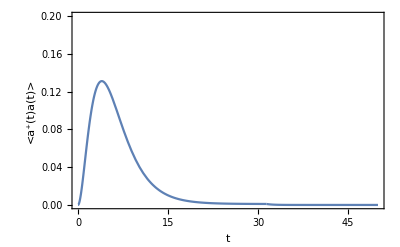

Brightness: 1.01453

```mathematica
(* Brightness for square pulse *)
par={γue->0.001,γde->1.,γs->0.05,χud->0.001,χdu->0.001,χs->0.01,Δ->0.001,Ω->0.5,tp->10.π};
drive=Expect[liou/.par,{0,istate},{{t,numberOp}}/.par];
decay=Expect[liou/.Ω->0/.par,{tp/.par,SuperU[liou/.par,tp/.par,0].istate},{{t,numberOp}}/.par];
exactplot=Show[
Plot[-1,{t,0,50},Frame->True,FrameLabel->{"t","<a^+(t)a(t)>"},BaseStyle->16,PlotRange->{0.,0.2}],
Plot[Abs[drive],{t,0.,tp/.par},PlotRange->{0,All}],
Plot[Abs[decay],{t,tp/.par,50},PlotRange->{0,All}]
]
Print["Brightness: ",brightnessN= NIntegrate[drive,{t,0,tp/.par}]+NIntegrate[decay,{t,tp/.par,∞}]]
```

### Example 2 : indistinguishability

- The Expect function only works for time independent systems. 
 - If the system is piecewise time independent, then we can use the function to compute expectation values, as in example 1 with a square pulse.
 - Mutli-time correlation functions, however, become complicated due to the number of time orders. For a two-time correlation with a two-piece time independent system (i.e. square pulse), we can use the TwoTimeTwoPiece algorithm.

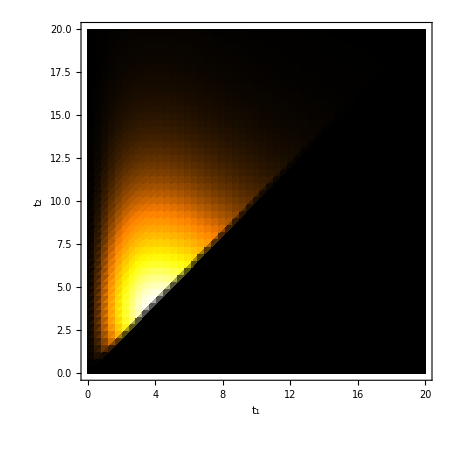

Indistinguishability: 0.85081

```mathematica
liou0=liou/.par;(* pulse on *)
liou1=liou/.Ω->0/.par; (* pulse off *)
fieldOp0=Sqrt[γde]*LFOp[σde,IdentityMatrix[Length[σde]]]/.par; (* annihilation LHS *)
fieldOp1=Sqrt[γde]*LFOp[IdentityMatrix[Length[σde]],ConjugateTranspose[σde]]/.par; (* creation RHS *)

{case1,case2,case3}=TwoTimeTwoPiece[{liou0,liou1},tp/.par,{0,istate},{{t,fieldOp0},{τ,fieldOp1}}];
cf[z_]:=Blend[{Black,Orange,Yellow,White},z];DensityPlot[
If[(t<tp/.par)&&( t<τ<tp/.par),Abs[case3]^2,
If[(t<tp/.par)&&(t<τ≥tp/.par),Abs[case2]^2,
If[(t≥tp/.par)&&(t<τ≥tp/.par),Abs[case1]^2,0]]],
{t,0,20},{τ,0,20},AspectRatio->1,ImageSize->450,PlotRange->{0,All},ColorFunction->cf,PlotPoints->50,FrameLabel->{"t_1","t_2"},BaseStyle->16]
num=NIntegrate[Abs[case1]^2,{t,tp/.par,∞},{τ,t,∞}]+
NIntegrate[Abs[case2]^2,{t,0,tp/.par},{τ,tp/.par,∞}]+
NIntegrate[Abs[case3]^2,{t,0,tp/.par},{τ,t,tp/.par}];
den=brightnessN^2/2;
Print["Indistinguishability: ",indistinguishabilityN=num/den];
```

### Example 3: 2nd-Order Correlation (single-photon purity)

Similar to indistinguishability, we can compute the second-order intensity correlation to quantify the single-photon purity.

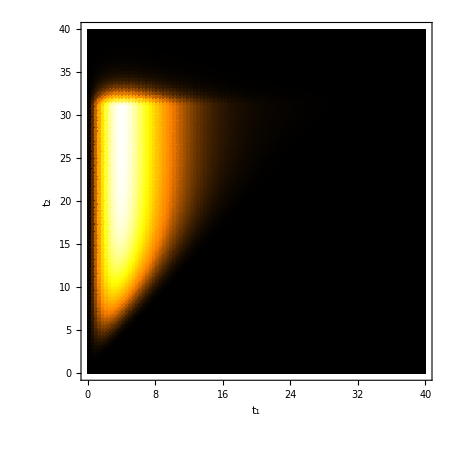

Single-photon purity: 0.961466

```mathematica
liou0=liou/.par;
liou1=liou/.Ω->0/.par;

{case1,case2,case3}=TwoTimeTwoPiece[{liou0,liou1},tp/.par,{0,istate},{{t,numberOp},{τ,numberOp}}/.par];

cf[z_]:=Blend[{Black,Orange,Yellow,White},z];DensityPlot[
If[(t<tp/.par)&&( t<τ<tp/.par),Abs[case3],
If[(t<tp/.par)&&(t<τ≥tp/.par),Abs[case2],
If[(t≥tp/.par)&&(t<τ≥tp/.par),Abs[case1],0]]],
{t,0,40},{τ,0,40},AspectRatio->1,ImageSize->450,PlotRange->{0,All},ColorFunctionScaling->True,ColorFunction->cf,PlotPoints->100,FrameLabel->{"t_1","t_2"},BaseStyle->16]
num=NIntegrate[Abs[case1],{t,tp/.par,100.},{τ,t,100.}]+
NIntegrate[Abs[case2],{t,0,tp/.par},{τ,tp/.par,100.}]+
NIntegrate[Abs[case3],{t,0,tp/.par},{τ,t,tp/.par}];
den=brightnessN^2/2;
Print["Single-photon purity: ",sppurityN=1-num/den];
```